```mathematica
SetDirectory@NotebookDirectory[]
```

/media/Storage

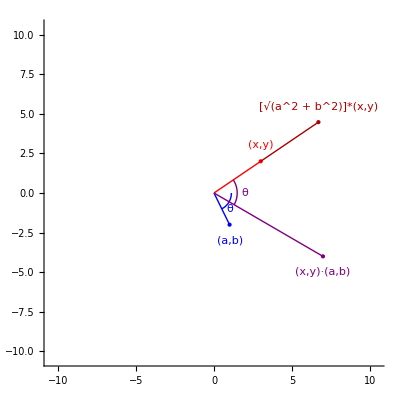

```mathematica
x=3;
y=2;
a=1;
b=-2;
r=Sqrt[a^2+b^2];
t=Arg[a+b I];
{u,v}={x a-y b,x b+a y};
size=10.5;
offset={0,1};
hoffset={0.5,0};
Graphics[{PointSize@Large,Red,Line@{{0,0},{x,y}},Point@{x,y},Inset["(x,y)",{x,y}+offset],Blue,Circle[{0,0},r/2,{0,t}],Line@{{0,0},{a,b}},Point@{a,b},Inset["(a,b)",{a,b}-offset],Inset["θ",{a,b}/2+hoffset],Purple,Circle[{0,0},r /1.5,{Arg[x+I y],Arg[u+I v]}],Inset["θ",{2,0}],Line@{{0,0},{u,v}},Point@{u,v},Inset["(x,y)·(a,b)",{u,v}-offset],Darker@Red,Line@{{x,y},{r x,r y}},Point@{r x,r y},Inset["[√(a^2 + b^2)]*(x,y)",r{x,y}+offset]},Axes->True,PlotRange->{{-size,size},{-size,size}}]
```

```mathematica
p[z_]:={Re@z,Im@z};
x=I-2;
y=5+5I;
u=(x+y)/2;
a=-0.35;
f=Interpolation[{{0,x},{1,y},{1/2,u+a I(y-x)}},InterpolationOrder->2];
g[t_]:=x+t(y-x)+I t Sin[10 Pi t];
size=10;
image[s_]:=Show[Graphics[{Red,PointSize@Large,Point[p/@{x,y}]}],ParametricPlot[p/@{f[t],g[t]},{t,0,1},PlotStyle->{Black,Dashed}],ParametricPlot[p[(1-s)f[t]+s g[t]],{t,0,1}],PlotRange->{{-size,size},{-size,size}},Axes->True];
Manipulate[image[s],{s,0,1}]
```

```mathematica
ds=0.025;
frames=image/@Range[0,1,ds];
Export["homotopy.gif",frames]
```

homotopy.gif

```mathematica
Clear[t,r];
dt=0.1;
r=1.2;
big[t_]:=Style[t,Large];
real={Inset[big@ℝ,{-5.5,5}],Line[{{-5,5},{5,5}}],Line[{{4.75,5.25},{5,5}}],Line[{{4.75,4.75},{5,5}}],Line[{{-4.75,5.25},{-5,5}}],Line[{{-4.75,4.75},{-5,5}}],Line[{{#,5.25},{#,4.75}}]&/@Range[-4,4],Inset[0,{0,5.5}],Red,Arrow@{{0,5},{2,5}}};
interval={Inset[big@"[0,1]",{-4.25,0}],Line[{{-3.5,0},{-1.5,0}}],Line[{{-3.5,.25},{-3.5,-.25}}],Line[{{-1.5,.25},{-1.5,-.25}}],Red,Arrow@{{-3.5,0},{-1.5,0}}};
circle={Inset[big@"S^1",{4.25,0}],Circle[{2.5,0}],PointSize@Large,Red,Point@{3.5,0},Arrow@Table[r/(r+(1-r)t/(4Pi)){Cos@t,Sin@t}+{2.5,0},{t,0,4Pi,dt}]};
arrowf={Arrow[BSplineCurve[{{-2.5,0.5},{0,3},{2,1.1}}]],Inset["f",{0,1.5}]};
arrowF={Arrow[BSplineCurve[{{-2.5,1},{-0.5,3},{0,4.5}}]],Inset["f^∼",{-1.5,3}]};
arrowp={Arrow[BSplineCurve[{{0.5,4.5},{5,3},{2.5,1.5}}]],Inset["p",{3.5,3}]};
Graphics[{real,,interval,circle,arrowf,arrowF,arrowp},ImageSize->Large]
```

-Graphics-

```mathematica
Clear[t,r,dt,r,big,real,interval,circle,arrowf,arrowF,arrowp];
dt=0.1;
r=1.2;
big[t_]:=Style[t,Large];
real[end_]:={Inset[big@ℝ,{-5.5,5}],Line[{{-5,5},{5,5}}],Line[{{4.75,5.25},{5,5}}],Line[{{4.75,4.75},{5,5}}],Line[{{-4.75,5.25},{-5,5}}],Line[{{-4.75,4.75},{-5,5}}],Line[{{#,5.25},{#,4.75}}]&/@Range[-4,4],Inset[0,{0,5.5}],Red,Arrow@{{0,5},{2 end,5}}};
interval[end_]:={Inset[big@"[0,1]",{-4.25,0}],Line[{{-3.5,0},{-1.5,0}}],Line[{{-3.5,.25},{-3.5,-.25}}],Line[{{-1.5,.25},{-1.5,-.25}}],Red,Arrow@{{-3.5,0},{2end-3.5,0}}};
circle[end_]:={Inset[big@"S^1",{4.25,0}],Circle[{2.5,0}],PointSize@Large,Red,Point@{3.5,0},Arrow@Table[r/(r+(1-r)t/(4Pi)){Cos@t,Sin@t}+{2.5,0},{t,0,4end Pi,dt}]};
arrowf={Arrow[BSplineCurve[{{-2.5,0.5},{0,3},{2,1.1}}]],Inset["f",{0,1.5}]};
arrowF={Arrow[BSplineCurve[{{-2.5,1},{-0.5,3},{0,4.5}}]],Inset["f^∼",{-1.5,3}]};
arrowp={Arrow[BSplineCurve[{{0.5,4.5},{5,3},{2.5,1.5}}]],Inset["p",{3.5,3}]};
img[end_]:=Graphics[{real[end],,interval[end],circle[end],arrowf,arrowF,arrowp},ImageSize->Large];
Manipulate[img[s],{s,0,1}]
```

```mathematica
ds=0.025;
frames=img/@Range[0,1,ds];
Export["lift.gif",frames]
```

lift.gif